```mathematica
matrixA = {{5,10},{10,30}};
matrixB = {8,20};
matrixX = LinearSolve[matrixA, matrixB];
matrixX
{4/5,2/5}
```

```mathematica
(*Exercise 1*)
```

```mathematica
xNodes = {-3,-2,-1,0,1,2,3};
yNodes = {7,4,1,1,5,6,13};
sValue = Length[xNodes];
```

```mathematica
AMatrix =
 {
{∑_(i=1)^sValue 1,∑_(i=1)^sValue xNodes[[i]],∑_(i=1)^sValue xNodes[[i]]^2},
{∑_(i=1)^sValue xNodes[[i]],∑_(i=1)^sValue xNodes[[i]]^2,∑_(i=1)^sValue xNodes[[i]]^3},
{∑_(i=1)^sValue xNodes[[i]]^2,∑_(i=1)^sValue xNodes[[i]]^3,∑_(i=1)^sValue xNodes[[i]]^4}
};

AMatrix
{7,0,28}
{0,28,0}
{28,0,196}
```

```mathematica
BMatrix = 
{
∑_(i=1)^sValue yNodes[[i]],∑_(i=1)^sValue yNodes[[i]]*xNodes[[i]],∑_(i=1)^sValue yNodes[[i]]*xNodes[[i]]^2
};

BMatrix
{37,68,226}
{24,29,109}
{24,29,109}
```

```mathematica
XMatrix  = LinearSolve[AMatrix, BMatrix];
```

```mathematica
basePoly[x_] = XMatrix[[1]] +XMatrix[[2]]*x+XMatrix[[3]]*x^2;
basePoly[x]
11/7+(13 x)/14+(13 x^2)/14
```

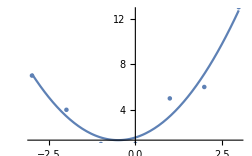
```mathematica
polyPloy = Plot[basePoly[x], {x, -3, 3}];
nodePlot = ListPlot[Transpose[{xNodes, yNodes}]];
Show[{polyPloy, nodePlot}]
-Graphics-
```

```mathematica
(*Exercise 2*)
```

```mathematica
f[x_] := x;
g[x_] := x^2;
fPlot=Plot[f[x], {x,0,1}];
gPlot = Plot[g[x], {x,0,1}];
```

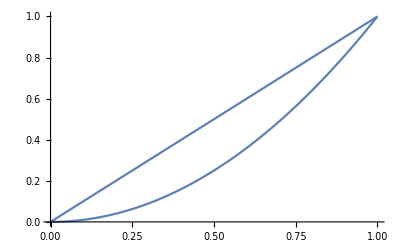

```mathematica
Show[{fPlot, gPlot}]
```

Checking how big the error is.

```mathematica
maxDiff= MaxValue[f[x]-g[x],x]
1/4
```

```mathematica
maxDiffWithOtherFormula = (Integrate[(f[x]-g[x])^2,{x,0,1}])^(1/2)
1/(√30)
```